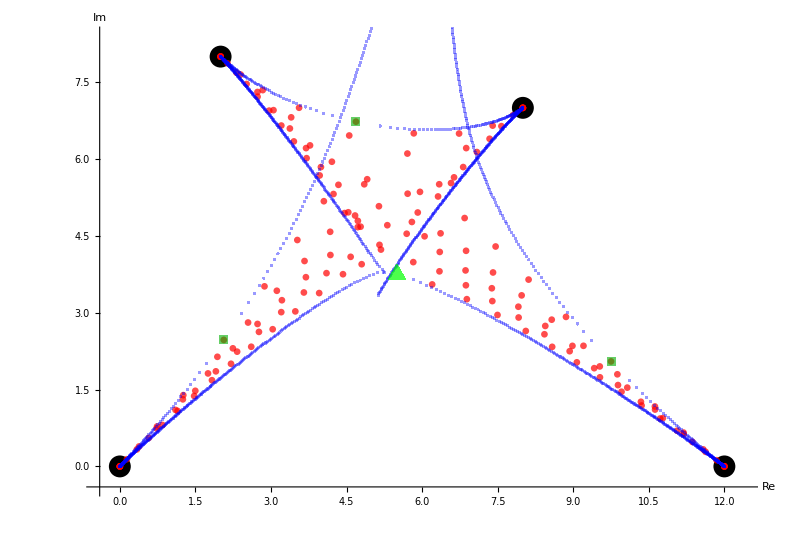

Shadow-n5.pdf

```mathematica
(* This program was used to create the plots of the polynomials shadows in Fig. 2 in the article "Rodrigues' Descendants of a Polynomial and Boutroux Curves", see https://doi.org/10.1007/s00365-023-09657-x *)

(* Choose the polynomial P and the exponent n. Nothing else needs to be changed *)
P=z (z-12) (z-2-8 I) (z-8-7 I);
n=15;

(* Finds the union of the roots of all orders of the derivative of P^n. Note that we remove the multiple roots at the zeros of P when m<n in order to speed up the computation of NSolve significantly *)
d=Exponent[P,z];
precision=10*d+n;
currentFunc=Expand[P^n];
roots={};
Do[roots=Join[roots,ReIm[z]/. NSolve[Simplify[currentFunc/(P^(n-m))]==0,WorkingPrecision->precision]];
currentFunc=D[currentFunc,z],{m,1,n-1}];
Do[roots=Join[roots,ReIm[z]/. NSolve[currentFunc==0,WorkingPrecision->precision]];
currentFunc=D[currentFunc,z],{m,n,n*d-1}];

(* Additional points for the final plot *)
rootsOfP=ReIm[z]/. NSolve[P==0,z,WorkingPrecision->precision];
rootsOfPPrime=ReIm[z]/. NSolve[D[P,z]==0,z,WorkingPrecision->precision];
centerOfMassOfZP=Mean[rootsOfP];

(* Determine branch points of equation (1.4) in the z-plane; a subset of these points serves as an appoximation of the boundary of the shadow *)
resStepLength=1/100; (* A smaller step length yields more branch points in the final plot *)
FF=Sum[((α-k)/k!) D[P,{z,k}] D[w^(d-k)],{k,0,d}];
RES=Resultant[FF,D[FF,w],w];

(* Attempt to calculate resultantRoots with error handling *)
resultantRoots={};
Do[rootsAttempt=Quiet[NSolve[RES==0/. α->αVal,z,WorkingPrecision->precision]];
If[rootsAttempt=!={},resultantRoots=Join[resultantRoots,ReIm[z]/. rootsAttempt]],{αVal,0+resStepLength,d-resStepLength,resStepLength}];

(* Draw the plot, and export it to Directory[] as a PDF file *)
rootRadius=Max[0.0015,(14054-Length[roots])/2265000];
convHullDims={Max[#]-Min[#]&/@Transpose[roots]};
rectSize=Max[convHullDims]/600;
critPointsRectSize=Max[convHullDims]/150;
s=Max[convHullDims]/35;

finalPlot=Show[Graphics[{{Black,PointSize[.02],Point[rootsOfP]},{Opacity[0.7],Red,PointSize[rootRadius],Point/@roots},{Opacity[0.4],Blue,PointSize[.0015],Rectangle[#-rectSize,#+rectSize]&/@resultantRoots},{Opacity[0.6],RGBColor[0,175/255,0],PointSize[.001],Rectangle[#-critPointsRectSize,#+critPointsRectSize]&/@rootsOfPPrime},{Opacity[0.7],RGBColor[0,1,0],PointSize[.0015],Triangle[{{#[[1]],#[[2]]+s/Sqrt[3]},{#[[1]]-s/2,#[[2]]-s/(2 Sqrt[3])},{#[[1]]+s/2,#[[2]]-s/(2 Sqrt[3])}}]&@centerOfMassOfZP}}],Axes->True,AxesLabel->{"Re","Im"},AspectRatio->Automatic,AxesOrigin->{Min[roots[[All,1]]]-Max[convHullDims]/30,Min[roots[[All,2]]]-Max[convHullDims]/30},PlotRange->{{Min[roots[[All,1]]]-Max[convHullDims]/30,Max[roots[[All,1]]]+Max[convHullDims]/30},{Min[roots[[All,2]]]-Max[convHullDims]/30,Max[roots[[All,2]]]+Max[convHullDims]/30}}]

(* Export the plot *)
Export[StringJoin["Shadow-n",ToString[n],".pdf"],finalPlot]
```